# Demo

```mathematica
SetDirectory@NotebookDirectory[];
assoc=Get["wickSATdata.txt"];
```

```mathematica
assoc // Keys
```

{wrapParams,timeStep,numBools,numParams,threshold,convergeTime,solProbEvo,expectedEnergyEvo,numRecoveries,recoveredIterations,param0Evo,param1Evo,param2Evo,param3Evo,param4Evo,param5Evo,param6Evo,param7Evo,param8Evo,param9Evo,param10Evo,param11Evo,param12Evo,param13Evo,param14Evo,param15Evo,param16Evo,param17Evo,param18Evo,param19Evo,param20Evo,param21Evo,param22Evo,param23Evo,param24Evo,param25Evo,param26Evo,param27Evo,param28Evo,param29Evo,param30Evo,param31Evo,param32Evo,param33Evo,param34Evo,param35Evo,param36Evo,param37Evo,param38Evo,param39Evo,param40Evo,param41Evo,param42Evo,param43Evo,param44Evo,param45Evo,param46Evo,param47Evo,param48Evo,param49Evo,param50Evo,param51Evo,param52Evo,param53Evo,param54Evo,param55Evo,param56Evo,param57Evo,param58Evo,param59Evo,param60Evo,param61Evo,param62Evo,param63Evo,param64Evo,param65Evo,param66Evo,param67Evo,param68Evo,param69Evo,param70Evo,param71Evo,param72Evo,param73Evo,param74Evo,param75Evo,param76Evo,param77Evo,param78Evo,param79Evo,param80Evo}

Vertical gray lines indicate where numerical approximation (e.g. TSVD) was used, since A was not invertible

```mathematica
assoc["timeStep"]
```

0.01

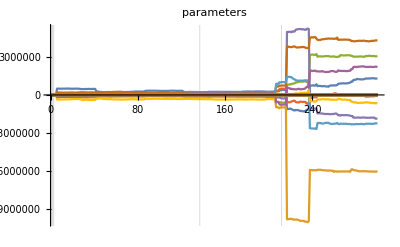

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	%, PlotRange->All, PlotLabel-> "parameters",
	 GridLines -> {assoc["recoveredIterations"], {}}
]
```

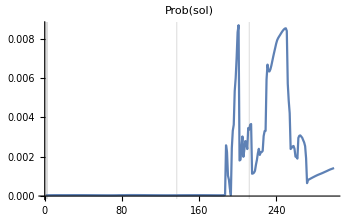

```mathematica
ListLinePlot[
	assoc["solProbEvo"], PlotLabel-> "Prob(sol)",
	GridLines -> {assoc["recoveredIterations"], {}}
]
```

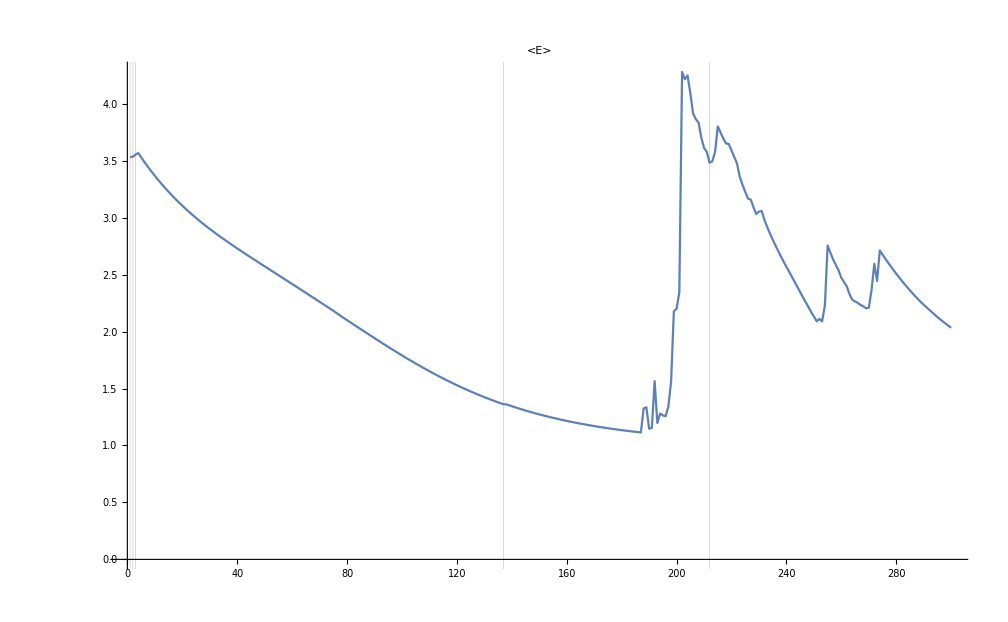

```mathematica
ListLinePlot[
	assoc["expectedEnergyEvo"], PlotLabel -> "<E>",
	GridLines -> {assoc["recoveredIterations"], {}}
]
```

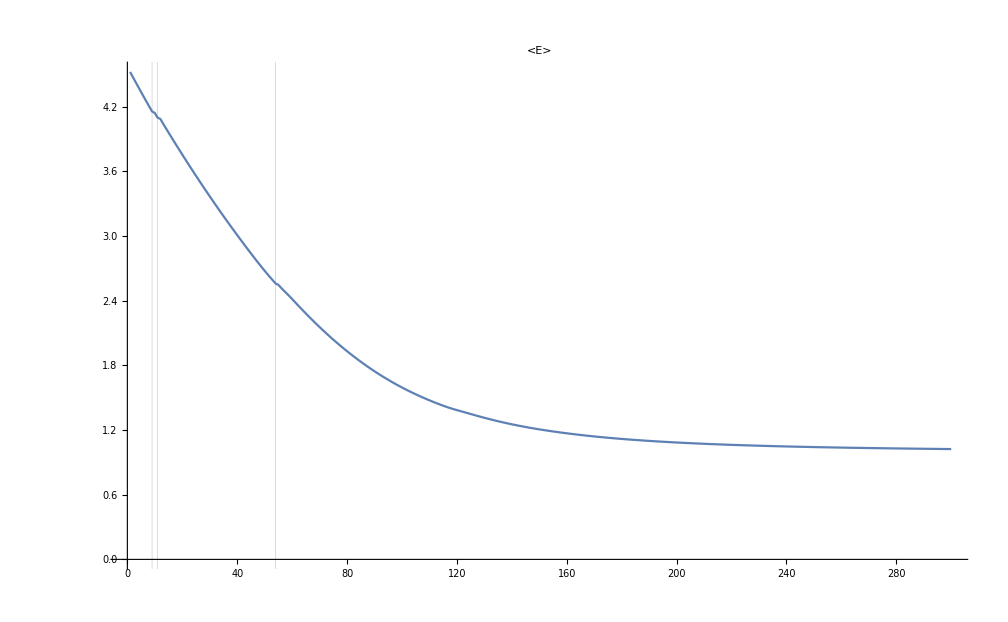

-Graphics-

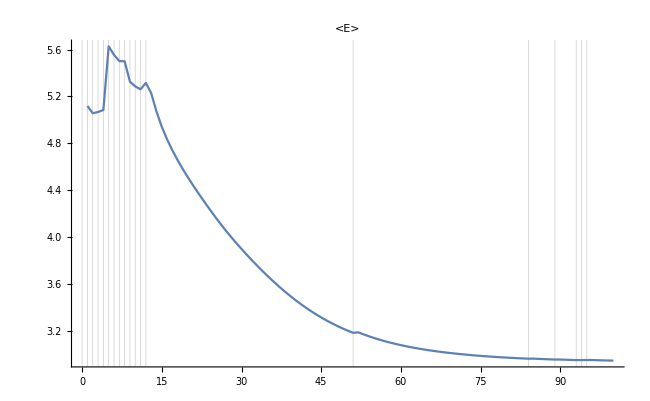

-Graphics-

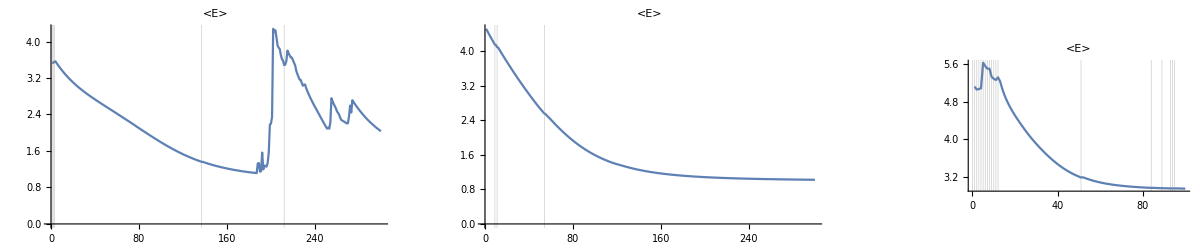

```mathematica
GraphicsRow[{%%%, %%, %}, ImageSize->Full]
```

well parameterised

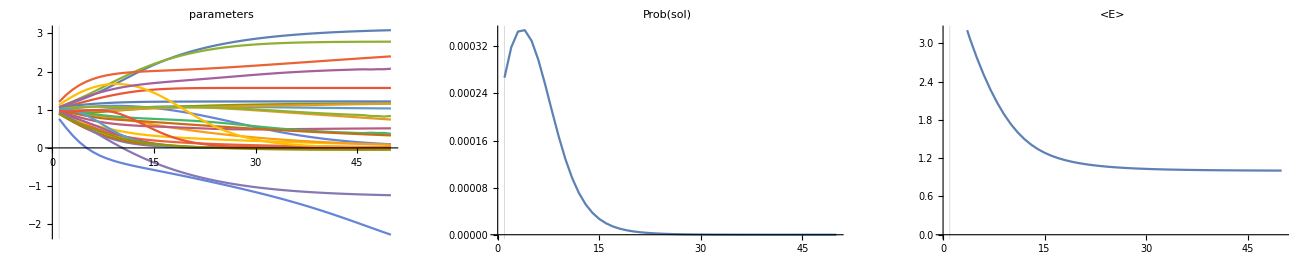

-Graphics-

well parameterised, starting in |+>

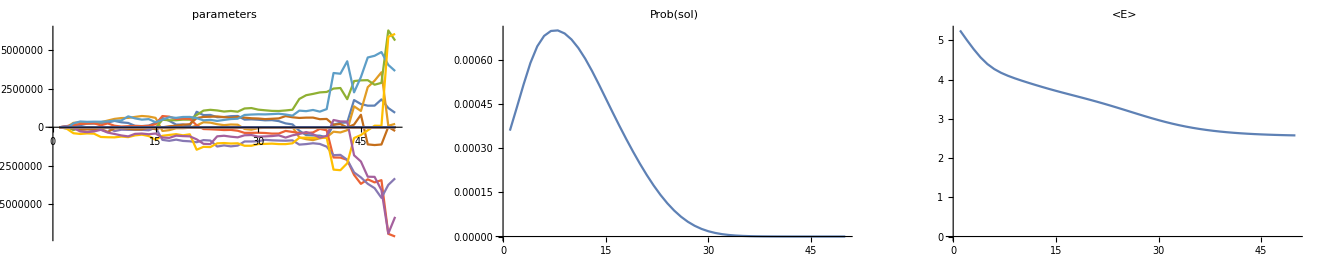

-Graphics-

under parameterised, uses TVSD

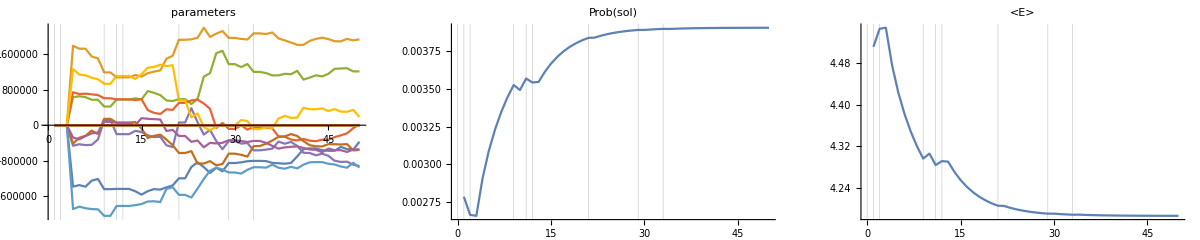

-Graphics-

well parameterised, big error in A

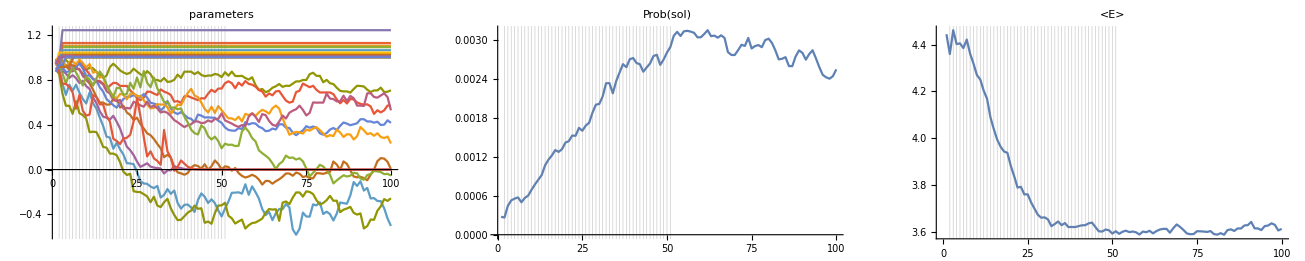

-Graphics-

# Analysis

```mathematica
discreteColors[n_]:=
	With[
		{partL=Ceiling[Sqrt[n]]},
		DeleteCases[Flatten[Transpose[Partition[Table[Lighter[Darker[Hue[c],.1],.25],{c,0,1-1/n,1/n}],partL,partL,1,0]]],0]
	]
```

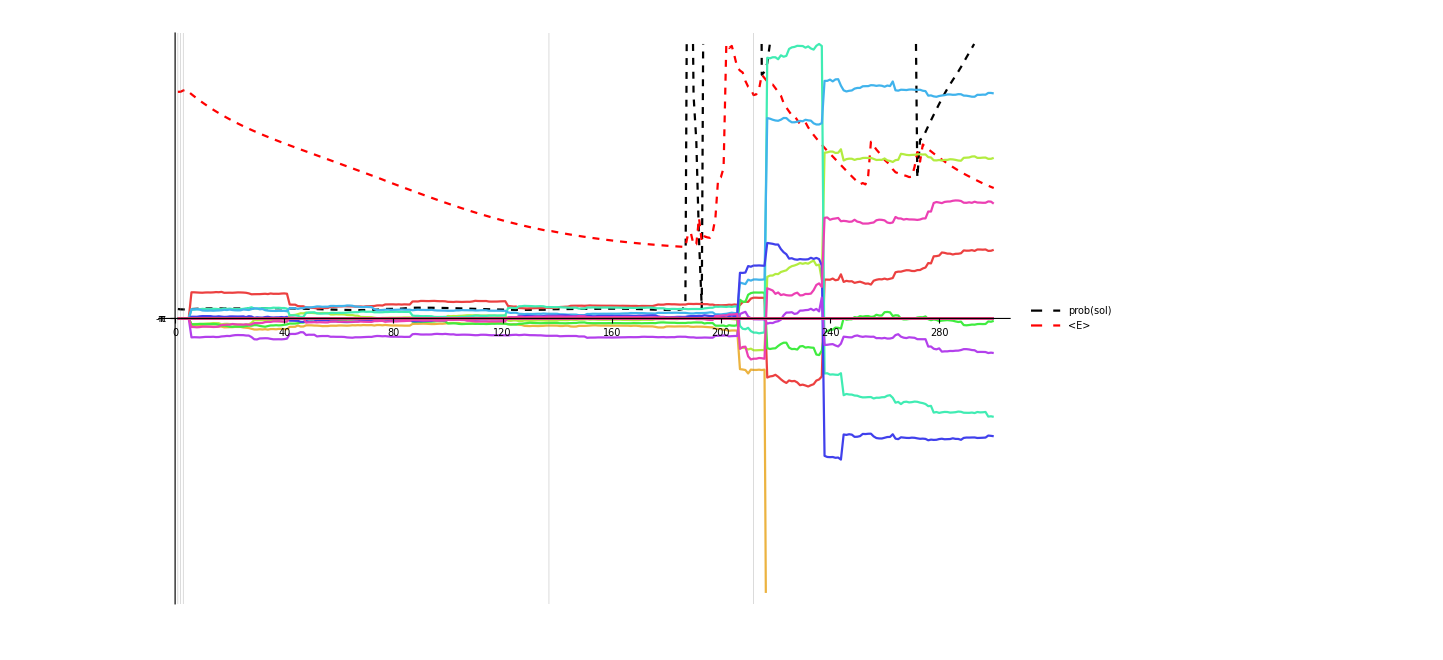

```mathematica
assoc[#]& /@ Table[
	StringJoin["param", ToString@p, "Evo"],
	{p, 0, assoc["numParams"]-1}
];
ListLinePlot[ 
	Join[
		{assoc["solProbEvo"]/Mean[assoc["solProbEvo"]]},
		{assoc["expectedEnergyEvo"]/Max[assoc["expectedEnergyEvo"]]},
		%/Max@%
	], 
	 GridLines -> {assoc["recoveredIterations"], {}},
	Ticks -> {Automatic,{{-π/Max@%, -π}, {π/Max@%, π}}},
	PlotStyle-> Join[{Directive[Black,Dashed], Directive[Red,Dashed]},discreteColors@Length@%],
	PlotLegends-> Placed[{"prob(sol)", "<E>"},{{.4,.8}}],
	PlotRange->{-1,1}
]
```